### Plot comparing kernel with/without full angular dependence

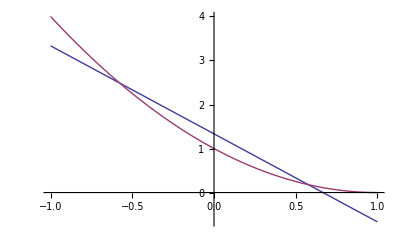

```mathematica
Plot[{
4/3 - 2*μ,
4/3 - 2*μ+2/3*1/2*(3μ^2-1)
},{μ,-1,1}]
```

### Define combinations of variables

Weak Interaction Constants

```mathematica
CV=1;
CA=1;
```

Equations C57-C61 and text above C66

```mathematica
y=(ω̄^2 ω^2 (1-μ)^2)/(ω̄^2+ω^2+2ω ω̄ μ)^(5/2);
AA=ω̄^2 y ((ω̄+ω μ)^2-1/2 ω^2 (1-μ^2));
BB=ω̄ y(-2 ω̄^2+ω^2+3ω ω̄-ω ω̄ μ+3ω^2 μ);
CC=y(ω̄^2+ω^2-3ω ω̄ - ω ω̄ μ);
DD=4Ee^2ω^2(1-μ^2)ω ω̄(1-μ)(-2Ee^2+2Ee(ω+ω̄)-ω ω̄(1-μ));
μ0=1-2Ee(ω+ω̄-Ee)/(ω ω̄);
f=(AA+BB Ee+CC Ee^2)LegendreP[l,μ];
```

Substitutions to make the integral easier

```mathematica
musub=(x^2-ω̄^2-ω^2)/(2 ω̄ ω);
xsub=Sqrt[ω̄^2+ω^2+2 ω̄ ω μ];
dmudx=D[musub,x];
```

Answers, just to check. b0 is different from C68 (I believe this is the units mistake mentioned in Evan’s code)

```mathematica
a0=1/(ω ω̄)(4/15 Ee^5-4/3Ee^4 ω̄+8/3Ee^3 ω̄^2);
b0=-a0+1/(ω ω̄)(8/3Ee^2(ω^3+ω̄^3)-4/3Ee(ω+ω̄)^2(3ω^2+ω̄^2-2ω ω̄)+4/15(ω+ω̄)^3(6ω^2+ω̄^2-3ω ω̄));
c0=ω^2/ω̄(8/3 ω̄^2+4 ω̄ ω+8/5ω^2)-Ee(16/3ω^2+4ω^3/ω̄)+8/3Ee^2 ω^2/ω̄;
d0=Simplify[4/15 ω̄^4/ω-4/3 ω̄^3/ω Ee+8/3 ω̄^2/ω Ee^2];
```

### Do the integrals

To change the coefficients we’re solving for, just change the value of l we’re replacing.

```mathematica
integrand=FullSimplify[f/.l->2]
```

1/(4 (ω^2+2 μ ω ω̄+(ω̄)^2)^(5/2))(-1+μ)^2 (-1+3 μ^2) ω^2 (ω̄)^2 (2 Ee^2 ω^2+ω̄ (2 Ee ω (-Ee (3+μ)+ω+3 μ ω)+ω̄ (2 Ee^2-2 Ee (-3+μ) ω+(-1+3 μ^2) ω^2+2 ω̄ (-2 Ee+2 μ ω+ω̄))))

Then, just execute the following. The commented integral works for the cases where the limits are {-1,1} but not when the limit is μ0. Even then, it takes a couple minutes to evaluate.

```mathematica
(*Integrate[%,{μ,-1,1},Assumptions->{μ≥-1,μ≤1,ω>0,ω̄>0,Ee>0,ω<ω̄}]*)
Simplify[integrand/.μ->musub,x>0];
Normal[Series[Expand[dmudx%],{x,0,100}]];
Simplify[Integrate[%,x]/.x->xsub];
a=Simplify[(%      /.μ->1)-(%       /.μ->μ0),{ω>0,ω̄>0,Ee>0,ω̄>ω>Ee}]
b=Simplify[(%%    /.μ->1)-(%%     /.μ->μ0),{ω>0,ω̄>0,Ee>0,Ee>ω>ω̄}]
c=Simplify[(%%%  /.μ->1)-(%%%  /.μ->-1),{ω>0,ω̄>0,Ee>0,ω̄>Ee>ω}]
d=Simplify[(%%%%/.μ->1)-(%%%%/.μ->-1),{ω>0,ω̄>0,Ee>0,ω>Ee>ω̄}]
```

1/(105 ω^3 (ω̄)^3)4 Ee^3 (6 Ee^4 (5 Ee^2-15 Ee ω+12 ω^2)-9 Ee^3 (20 Ee^2-52 Ee ω+35 ω^2) ω̄+Ee^2 (432 Ee^2-945 Ee ω+511 ω^2) (ω̄)^2-14 Ee (36 Ee^2-63 Ee ω+25 ω^2) (ω̄)^3+7 (36 Ee^2-45 Ee ω+10 ω^2) (ω̄)^4)

1/(105 ω^3 (ω̄)^3)4 (-Ee+ω+ω̄)^3 (6 (5 Ee^6-3 Ee^4 ω^2-4 Ee^3 ω^3-3 Ee^2 ω^4+5 ω^6)+9 Ee^2 (-10 Ee^3+2 Ee^2 ω+5 Ee ω^2+3 ω^3) ω̄+(72 Ee^4-45 Ee^3 ω-29 Ee^2 ω^2+3 Ee ω^3+6 ω^4) (ω̄)^2+(12 Ee^3+27 Ee^2 ω-5 Ee ω^2-6 ω^3) (ω̄)^3+(-18 Ee^2+9 Ee ω+7 ω^2) (ω̄)^4-9 (2 Ee+ω) (ω̄)^5+12 (ω̄)^6)

1/(105 (ω̄)^3)4 ω^2 (6 ω^2 (12 Ee^2-15 Ee ω+5 ω^2)+9 ω (7 Ee^2-20 Ee ω+10 ω^2) ω̄+(7 Ee^2-105 Ee ω+96 ω^2) (ω̄)^2-14 (Ee-3 ω) (ω̄)^3+7 (ω̄)^4)

(4 (ω̄)^2 (7 Ee^2 ω^2+7 Ee (9 Ee-5 ω) ω ω̄+2 (36 Ee^2-45 Ee ω+8 ω^2) (ω̄)^2+27 (-2 Ee+ω) (ω̄)^3+12 (ω̄)^4))/(105 ω^3)

```mathematica
J1=
(1/(ω̄ ω)HeavisideTheta[ω+ω̄-Ee]*(
a(HeavisideTheta[ω-Ee]HeavisideTheta[ω̄-ω]+
HeavisideTheta[ω̄-Ee]HeavisideTheta[ω-ω̄])+
b(HeavisideTheta[Ee-ω]HeavisideTheta[ω-ω̄]+
HeavisideTheta[Ee-ω̄]HeavisideTheta[ω̄-ω])+
c(HeavisideTheta[Ee-ω]HeavisideTheta[ω̄-Ee])+
d(HeavisideTheta[Ee-ω̄]HeavisideTheta[ω-Ee])
));
J2=J1/.ω̄->asdf/.ω->ω̄/.asdf->ω;
phi=Simplify[(CV+CA)^2J1+(CV-CA)^2J2];
```

Test to see whether the kernel value is nonzero

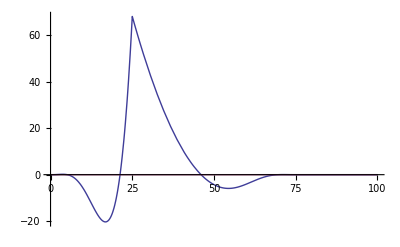

-61.5079

505.952

444.444

```mathematica
w=25;
wp=50;
Plot[{Simplify[phi/.ω̄->wp/.ω->w/.Ee->q],Simplify[phi/.ω̄->wp/.ω->w/.Ee->q+(w+wp)]},{q,0,100},PlotRange->Full]
NIntegrate[phi/.ω̄->wp/.ω->w/.Ee->q,{q,0,w},MaxRecursion->100]
NIntegrate[phi/.ω̄->wp/.ω->w/.Ee->q,{q,w,w+wp},MaxRecursion->100]
NIntegrate[phi/.ω̄->wp/.ω->w/.Ee->q,{q,0,w+wp},MaxRecursion->100]
```

```mathematica
phi0=%
```

4444.44

```mathematica
phi1=%
```

-2222.22

```mathematica
phi2=%
```

444.444

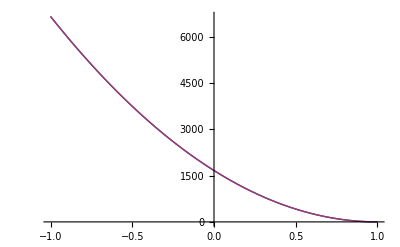

1666.67

1666.67

```mathematica
moments[x_]:=1/2 phi0 + 3/2 phi1 x + 5/2 phi2 1/2(3 x^2-1)
explicit[x_]:=1/2*3/4phi0(1-x)^2
Plot[{moments[x],explicit[x]},{x,-1,1}]
moments[0]
explicit[0]
```